## 1. 数据准备

### 1.1. 数据来源

Terra/Aqua卫星MODIS传感器数据反演所得的净初级生产力(NPP)逐年数据

产品MOD17A3H v006由美国地质调查局(USGS)生产和托管(DOI: 10.5067/MODIS/MOD17A3H.006)

int16类型

NPP结果单位为kg C/m.b2, 并缩小到10^-4倍

部分未计算NPP的像元根据性质被赋值32761~32767

### 1.2. 数据导入与异常值移除

时间范围 : 2004 年~2015 年

更正了异常值移除规则中的错误, 原有的异常值移除规则已被注释, 不再执行. (2024-09-19)

```mathematica
ts=Import[NotebookDirectory[]<>"../Source/MOD17A3H_Lyr_Stk.tif"]//ImageData[#,"Bit16"]&//Part[#,All,All,5;;16]&//Flatten[#,1]&;
ts-=32768;
(*ts=DeleteCases[ts,{_,(_?(#>32760&))..,_}];*)
ts=Select[ts,!MemberQ[#,_?(#>32760&)]&];
```

```mathematica
ts//Length
```

1338967

## 2. 仅考虑时间因素的回归模型

### 2.1. 利用前n年NPP预测下一年NPP: n元线性回归模型

#### 2.1.1. 训练样本选取

不放回随机抽取二十万个样本, 样本的空间分布完全随机, 抽取结果中十六万个样本被用作训练集, 四万个样本被用作测试集, 二者互斥.

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
tssmp=ts//RandomSample[#,200000]&//N;
train=tssmp[[1;;160000]];
test=tssmp[[160001;;-1]];
```

#### 2.1.2. 模型假设

每个像元所在位置, 在t_(n+1)时刻的NPP值, 只和该位置t_1, t_2, …, t_n时刻的NPP值有关, 与其他像元任何时间的NPP值均无关

参与模型训练的数据规模远大于模型的复杂程度, 不需要正则化

#### 2.1.3. 模型建立方法

使用训练集中的最后(n+1)年至最后2年的数据作为自变量, 最后一年的数据作为因变量, 构造n元线性回归模型

```mathematica
linRegSpat//ClearAll;
linRegSpat[year_]:=linRegSpat[year]=Block[{n=year,varReg,mdlReg},
	varReg=Table[Unique["x"],{n}];
	mdlReg=train[[All,-(n+1);;-1]]//LinearModelFit[#,varReg,varReg]&;
	Return[mdlReg];
];
```

计算回归结果R^2, 并绘制R^2与参与回归分析的数据年数n之间的关系图

{0.848504,0.855523,0.889383,0.889478,0.897886,0.900578,0.900581,0.900879,0.903732,0.903894}

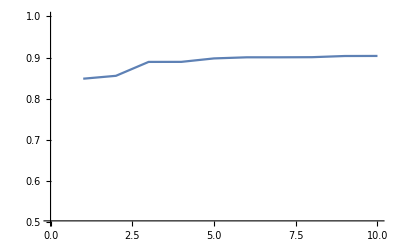

```mathematica
With[{linRegSpatR2=Table[linRegSpat[n]["RSquared"],{n,10}]},
	Print[linRegSpatR2];
	Print[ListPlot[linRegSpatR2,Joined->True,PlotRange->{{0, 10},{0.5,1}}]];
]
```

#### 2.1.4. 模型泛化能力测试

使用测试集中的最后(n+1)年至最后2年的数据作为自变量, 预报最后一年的数据

将预报结果与测试集中实际的数据比较, 计算RMSE

```mathematica
linRegSpatFunc//ClearAll;
linRegSpatFunc[year_]:=linRegSpatFunc[year]=linRegSpat[year]["Function"];
```

```mathematica
linRegSpatRMSE//ClearAll;
linRegSpatRMSE[year_]:=linRegSpatRMSE[year]=Block[{n=year,err,fn},
	fn=linRegSpatFunc[year];
	err=Map[(fn@@Most[#]-Last[#])&,test[[All,-(n+1);;-1]]];
	Return[err^2//Mean//Sqrt];
];
```

计算均方根误差RMSE, 并绘制RMSE与参与回归分析的数据年数n之间的关系图

{438.726,428.16,373.707,373.669,359.395,354.86,354.854,354.373,349.779,349.472}

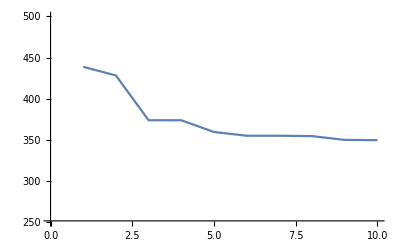

```mathematica
Print[Table[linRegSpatRMSE[n],{n,10}]];
Print[ListPlot[Table[linRegSpatRMSE[n],{n,10}],Joined->True,PlotRange->{{0, 10},{250,500}}]];
```

### 2.2. 分段趋势分析: 分段线性回归模型(拟合结果不用于预测)

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
smpReg=RandomSample[ts,20];
```

#### 2.2.1. 绝对值函数与一次函数的线性组合

考虑分段线性回归模型
y=Piecewise[{{k_0(x-x_1)+y_1, x<x_1}, {k_1(x-x_1)+y_1, x≥x_1}}], (k_0,k_1∈ℝ)
该回归方程可视为y=1, y=x, 以及y=|x-x_1|三者的线性组合.

在给定分段点横坐标x_1的情况下, 可以确定回归模型中的三个参数. 但不同的x_1拟合效果不同.

```mathematica
linpwReg//Clear;
linpwReg[tser_,x1_]:=Block[{x},LinearModelFit[tser,{1,x,Abs[x-x1]},x]]
```

要寻找最佳的分段点, 需要建立回归方程R^2与x_1的关系, 并通过最优化算法, 求得使R^2取最大时的x_1

```mathematica
linpwRegRsq//Clear;
linpwRegRsq[tser_,x1_]:=Block[{x,fn,residue},
	Return[linpwReg[tser,x1]["RSquared"]];
];
```

最优化算法是基于迭代的, 不能并行化.

```mathematica
perfMax=Table[Table[Flatten[{FindMaximum[linpwRegRsq[smpReg[[idx]],x1],{x1,6.5},Method->mthd]//AbsoluteTiming},2],{mthd,{Automatic,"ConjugateGradient","PrincipalAxis","LevenbergMarquardt","Newton","QuasiNewton"}}],
{idx,1,smpReg//Length,1}];
```

```mathematica
(perfMax[[All,1,1]]//Mean)*10000
```

3276.2

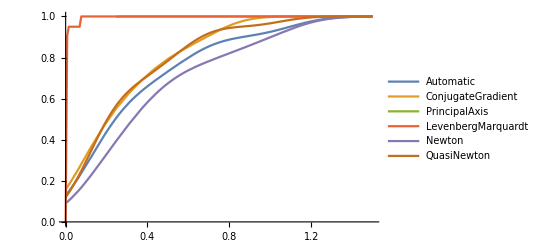

```mathematica
perfMax[[All,All,1]]//Transpose//SmoothHistogram[#,Automatic,"CDF",PlotRange->{{0,1.5},{0,1}},PlotLegends->{{Automatic,"ConjugateGradient","PrincipalAxis","LevenbergMarquardt","Newton","QuasiNewton"}}]&
```

当时相数目为12时, 估测每十次优化的平均开销达到了秒级(LevenbergMarquardt方法发生了迭代中断, 返回的结果仍然在迭代初值附近, 对本问题无效), 对于常用的时序产品, 其像元数目一般在10^5至10^8的数量级, 处理时间预计可达数日, 效率过低, 因此需要采用其他方法.

#### 2.2.2. 引入虚拟变量^[1], 将分段回归转化为二元回归^[1]

参考文献: 
	[1]孔凡胜. 西藏旅游人口的分段回归分析[J]. 现代商贸工业, 2019, 40(03): 24-25. DOI:10.19311/j.cnki.1672-3198.2019.03.011.
	[2]高璇, 赵东升, 郑度. 1961～2018年中国地表温度变化的区域差异[J]. 大气科学, 2023, 47(04): 995-1006.

分段线性回归的方程可做如下变形^[1-2]: 
y=Piecewise[{{β_0+β_1 x, x≤x_1}, {β_0+β_1 x+β_2(x-x_1), x>x_1}}],

令{ξ_1=x
ξ_2=max(x-x_1,0), 则上式变形为ξ_1, ξ_2 关于的二元线性回归方程^[1-2]
y=β_0+β_1 ξ_1+β_2 ξ_2

但是, 上述方法需要通过人工判读数据的总体趋势^[2], 或者分析影响趋势的外部因素^[1], 手动确定分段点的横坐标, 于是上述问题转化为2.2.1中的问题. 需要寻找一种高效的自适应搜索分段点横坐标的方法.

#### 2.2.3. 基于新引入参数^[3-4]的分段点搜索算法(Muggeo法)

参考文献: 
	[3]MUGGEO V. Estimating Regression Models with Unknown Break-Points[J]. Statistics in medicine, 2003, 22: 3055-3071. DOI:10.1002/sim.1545.
	[4]MUGGEO V M R. segmented: An R package to Fit Regression Models with Broken-Line Relationships[J]. R News, 2008, 8(1): 20–25.

一种思路是: 向回归方程中引入一个新参数^[3-4], 用于在迭代过程中, 动态搜寻分段点

分段线性回归方程 
y=Piecewise[{{β_0+β_1 x, x≤x_1}, {β_0+β_1 x+β_2(x-x_1), x>x_1}}] 等价于y=β_0+β_1 x+β_2·(x-x_1) ·step(x-x_1), 
其中step(ξ)=Piecewise[{{0, ξ≤0}, {1, ξ>0}}]

引入新参数构造新的回归方程 y=β_0+β_1 x+β_2·(x-x_1) ·step(x-x_1)+γ_2·step(x-x_1)

令{ξ_1=x
ξ_2=max(x-x_1,0)
ξ_3=step(x-x_1), 则上式变形为关于ξ_1, ξ_2, ξ_3 的三元回归方程^[3]
y=β_0+β_1 ξ_1+β_2 ξ_2 +γ_2 ξ_3

初始化x_00, 随后执行迭代

将x_(0i)代入回归方程, 得到参数β_(0i), β_(1i), β_(2i), γ_(2i),

利用模型参数调整分段点^[3-4]: 令x_(0(i+1))=x_(0i)-γ_(2i)/β_(2i)

迭代终止的条件: ||γ_(2i)/β_(2i)||小于某一阈值^[3-4], 或者迭代执行次数达到了预设的上限

```mathematica
linpwRegMuggeo//Clear;
linpwRegMuggeo[tser_List,x1_Integer]:=Block[{tserMulvar},
	tserMulvar=MapIndexed[{#2[[1]],Max[#2[[1]]-x1,0],Boole[#2[[1]]>x1],#1}&,tser];
	Return[tserMulvar];
];
```

```mathematica
linpwRegMuggeoIter//Clear;
linpwRegMuggeoIter[tser_List]:=Block[{x,y,z,tserMulvar,mdl,coef,x1,β2,γ2,dispList,dispAccu},
x1=(1+tser//Length)/2;
(*Start iteration, meanwhile gather break-points and differences from every steps*)
dispList=Reap[
Do[
	(*Establish regress model*)
	tserMulvar=linpwRegMuggeo[tser,x1];
	mdl=Fit[tserMulvar,{1,x,y,z},{x,y,z}];
	(*Gather coefficent*)
	coef=mdl//Coefficient[#,{x,y,z}]&;
	{β2,γ2}=coef[[{2,3}]];Sow[{x1,γ2/β2}];
	(*Update segment break-point*)
	x1-=γ2/β2;
	(*Terminate iteration ahead of time if certain conditions are met*)
	If[β2==0||γ2==0||x1<1||x1>(tser//Length)||Abs[γ2/β2]≤0.01,
		Break[]];
,{iter,32}]
][[2,1]];
(*Handle results if iteration cycles*)
If[MemberQ[dispList//Most,dispList//Last],
	(*Identify step from which iteration cycles*)
	dispList=dispList//Reverse;dispAccu=dispList[[All,2]]//Accumulate;
	dispList=dispList//Take[#,LengthWhile[dispAccu,Abs[#]>0.01&]]&;
	(*Filter all break-points in the cycle*)
	dispList=Join[dispList[[All,1]],{x1}];
	(*Find the fittest model*)
	tserMulvar=linpwRegMuggeo[tser,#]&/@dispList;
	mdl=LinearModelFit[#,{1,x,y,z},{x,y,z}]["RSquared"]&/@tserMulvar;
	x1=dispList[[Ordering[mdl,-1]]]//First;
];
Return[x1];
];
```

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
smpReg=RandomSample[ts,100];
```

```mathematica
perfMuggeo=Table[
	AbsoluteTiming[linpwRegMuggeoIter/@smpReg][[1]],
{25}];
```

```mathematica
(perfMuggeo//Mean)*100
```

31.574

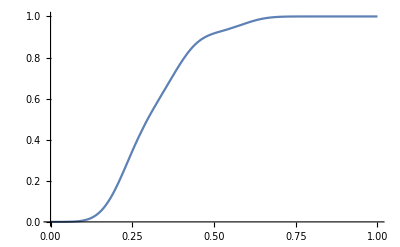

```mathematica
SmoothHistogram[perfMuggeo,Automatic,"CDF",PlotRange->{{0,1},{0,1}}]
```

当时相数目为12时, 估测每千次优化的平均开销达到了秒级, 相同规模的数据, 在此方法下的处理时间, 比前述方法降低了两个数量级.

该模型同样适用于回归方程具有多个分段点的情况. 设n个分段点分别为x_1, x_2, …,x_n,  引入参数前后的回归方程分别为
y=β_0+β_1 x+β_2·(x-x_1) ·step(x-x_1)+…+β_(n+1)·(x-x_n) ·step(x-x_n)
和
y=β_0+β_1 x+β_2·(x-x_1) ·step(x-x_1)+γ_2·step(x-x_1)+…+β_(n+1)·(x-x_n) ·step(x-x_n)+γ_(n+1)·step(x-x_n)

迭代方法与单一分段点的情况相同.

```mathematica
linpwRegMuggeoN//Clear;
linpwRegMuggeoN[tser_List,xSeg_List]:=Block[{tserMulvar},
	tserMulvar=MapIndexed[
		Flatten@Join[#2[[1]]//List,Table[{Max[#2[[1]]-x,0],Boole[#2[[1]]>x]},{x,xSeg}],{#1}]&
	,tser];
	Return[tserMulvar];
];
```

```mathematica
linpwRegMuggeoNIter//Clear;
linpwRegMuggeoNIter[tser_List,n_Integer]:=
Block[{varReg,tserMulvar,mdl,coef,
	xSeg,βSeg,γSeg,disp,dispList,dispAccu,nCycle},
	(*In case of n=1, use previous iteration method*)
	If[n==1,
		xSeg={linpwRegMuggeoIter[tser]};
		Return[xSeg];
	];
	(*Generate partition break-points uniformly*)
	xSeg=Range[0,1,1./(n+1)]//Rescale[#,{0,1},{1,tser//Length}]&//Part[#,2;;-2]&;
	(*Generate variables for regression*)
	varReg=Table[Unique["x"],{2n+1}];
	(*Start iteration, meanwhile gather break-points and differences from every steps*)
	dispList=Reap[
	Do[
		(*Establish regress model*)
		tserMulvar=linpwRegMuggeoN[tser,xSeg];
		mdl=Fit[tserMulvar,Join[{1},varReg],varReg];
		(*Gather coefficent*)
		coef=mdl//Coefficient[#,varReg]&;
		βSeg=coef[[2;;-1;;2]];γSeg=coef[[3;;-1;;2]];
		disp=γSeg/βSeg;Sow[{xSeg,disp}];
		(*Update segment break-point*)
		xSeg-=disp;
		(*Terminate iteration ahead of time if certain conditions are met*)
		If[Positive@Count[βSeg,0]||Positive@Count[γSeg,0]||
		Positive@Count[xSeg,_?((#<1||#>Length[tser])&)]||Norm[disp]≤0.01,
		Break[]];
	,{iter,32}]
	][[2,1]];
	(*Identify step from which iteration cycles*)
	dispList=dispList//Reverse;dispAccu=dispList[[All,2]]//Accumulate;
	nCycle=LengthWhile[dispAccu,Norm[#]>0.01&];
	(*Handle results if iteration cycles*)
	If[nCycle<Length[dispList],
		dispList=dispList//Take[#,nCycle]&;
		(*Filter all break-points in the cycle*)
		dispList=Join[dispList[[All,1]],{xSeg}];
		(*Find the fittest model*)
		tserMulvar=Map[linpwRegMuggeoN[tser,#]&,dispList];
		mdl=LinearModelFit[#,Join[{1},varReg],varReg]["RSquared"]&/@tserMulvar;
		xSeg=dispList[[Ordering[mdl,-1]]]//First;
	];
	Return[xSeg];
];
```

```mathematica
perfMuggeoN=Table[
	AbsoluteTiming[linpwRegMuggeoNIter[#,n]&/@smpReg][[1]],
{i,25},{n,4}];
```

```mathematica
(perfMuggeoN//Mean)*100
```

{28.579,22.277,15.974,15.163}

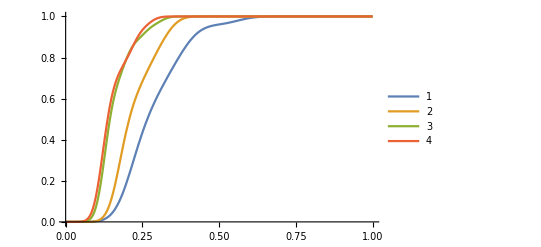

```mathematica
SmoothHistogram[perfMuggeoN//Transpose,Automatic,"CDF",PlotRange->{{0,1},{0,1}},PlotLegends->Range[4]]
```

在GIthub可检索到一系列具有分段回归功能的程序包. 其中, 由Google维护的pwlfit项目中, 提供了分段回归的分段点自适应搜索功能.

上述项目由Python编写. 由于本课程的项目将在IDL上实现, 需要将项目的主要代码全部转化为IDL代码.

本课程项目将以2021年7月21日的提交版本为准 (修改于2024-09-22) 以2020年7月28日的第2次提交版本为准. 主要原因是:

该版本是最后一版在注释中详细提供了与Py 2.x兼容性有关内容 (修改于2024-09-22) 兼容Python 2.x的版本.

考虑到项目所依托的ENVI 5.3/IDL 8.5 以及对应的IDL Python Bridge, 可能与ArcGIS Desktop 10.5 的arcpy一同被集成至独立的python 2. x环境下使用,

代码中需要注明源代码的来源.

## 3. 时间序列特征提取

### 3.1. 自相关系数

当时间序列包含的时相数量在10~100的数量级时, 时间序列的周期性变化特征一般不能使用FFT方法提取, 主要原因:

在边缘附近容易出现Gibbs效应

如作加窗处理, 易导致失真.

采用各阶自相关函数分析时间序列的波动特征, 并识别出各像元时间序列中, 自相关函数最大的阶.

```mathematica
tsAutoCorr=ParallelTable[CorrelationFunction[smp,{1,10}],{smp,train}];
```

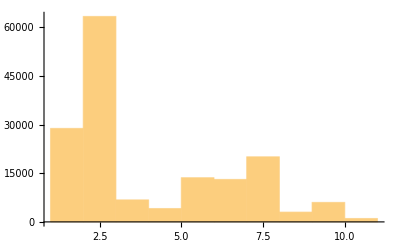

```mathematica
Position[#,Max[#]][[1,1]]&/@Select[tsAutoCorr,AnyTrue[#,Positive]&]//Histogram[#,LabelingFunction->None]&
```